# Dados do Circuito de Linhas de Transmissão Aéreas

Antonio Carlos Siqueira de Lima
Eletromagnetismo II
Departamento de Engenharia Elétrica
Escola Politécnica, POLI/UFRJ

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/Transmissão-2020

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 83854 10^-12;
σs=10.0^-3;
ℓ=80 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 100.0;
```

## Circuito 138kV

```mathematica
rf=7.1501*10^-3;
rint=2.3876*10^-3;
Rdc=35.356020838304296*10^-5 ;
ρc=Rdc* π* (rf^2-rint^2);
```

```mathematica
xc={-3.8,3.8,-3.8,-2.4,2.4};
yc={28.1,31.1,28.1+5.9, 28.1+5.9+7.8,28.1+5.9+7.8};
fl={14.6,14.6,14.6,8.7,8.7};
yc=yc-2/3 fl;
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 0.5,PlotRange->{{-10,10},{5,40.}},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

## Circuito de 500kV

### cabo de fase

```mathematica
rf=29.591*10^-3/2;
rint=7.3914*10^-3/2; 
ρc=6.114292531162*10^-5 * π* (rf^2-rint^2);
```

### cabo pararraio

```mathematica
rpr=4.57*10^-3;
ρpr= π  *4.19*10^-3*rpr^2;
```

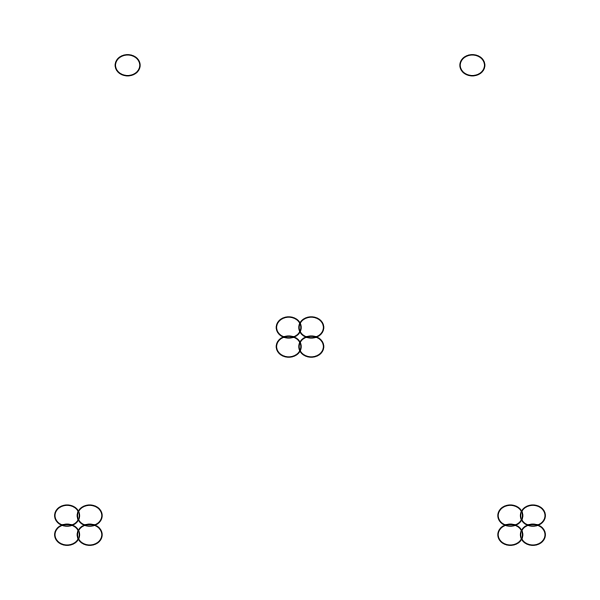

```mathematica
xy4= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229},
 {-4.729, 10.771}, {0.229, 15.271},{0.229, 15.729},
 {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771},
 {4.271, 11.229},{4.729, 11.229},{4.729, 10.771},
 {-3.500, 22.000}, {3.500, 22.000}};

xc= xy4[[All,1]];
yc=xy4[[All,2]];
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.25]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{"Distance [m]","Distance [m]"}]
```

## Circuito de 345kV

pode-se considerar os mesmos condutores que no caso de 500 kV

```mathematica
xy1={{-7.229,10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 10.500}, {7.229, 10.500},
{6.771, 10.500}, {-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra1={Circle[#,.25]}&/@xy1;
```

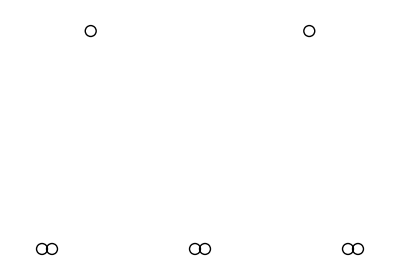

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}]
```

## Circuito duplo 500kV

são os mesmos cabos pararraios dos casos anteriores

### cabo de fase

```mathematica
rint=0.003995;
rf=0.01598;
Rdcϕ=0.000051;
ρϕ= Rdcϕ*Pi*(rf^2-rint^2);
```

coordenadas do centro do feixe, sabendo que o espaçamento entre condutores é de 45,7 cm

```mathematica
xy={{6, 35-2/3 25.8 },{6, 35 +10 -2/3 25.8},{6, 35+20-2/3 25.8},
{-6, 35-2/3 25.8 },{-6, 35 +10 -2/3 25.8},{-6, 35+20-2/3 25.8},
{8.5, 35+20+8.5 -2/3 13},{-8.5, 35+20+8.5 -2/3 13}};
xc= xy[[All,1]];
yc=xy[[All,2]];
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.25]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,PlotRange->Automatic,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{"Distance [m]","Distance [m]"}]
```

-Graphics-

## Circuito não convencional de 500kV

```mathematica
rf=7.3914*10^-3/2;   (* ⟹ [m] ⟸ *)
rint=29.591*10^-3/2;
Rdcϕ=6.114292531162*10^-5;  (* ⟹ [Ω/m] ⟸⟹ @ 25^o ⟸*)
ρϕ=Rdcϕ*Pi*(rf^2-rint^2);
```

```mathematica
xy5={{-5.754,9.543},{-4.496,10.314},{-4.977,11.562},{-6.529,11.562},{-7.009,10.314},{0.000,13.845},{0.866,14.409},{0.535,15.317},{-0.535,15.317},{-0.866,14.409},{5.754,9.543},{4.496,10.314},{4.977,11.562},{6.529,11.562},{7.009,10.314},{-4.000,23.961},{4.000,23.961}};
```

```mathematica
xc= xy5[[1;;,1]];
```

```mathematica
yc= xy5[[1;;,2]];
```

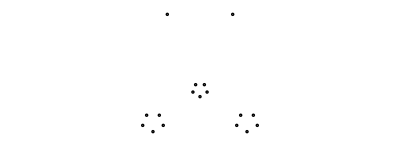

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-20,20},All},FrameTicks->{{-10,0,10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```